```mathematica
amplitude[t_, dd_, ωω_]:=Module[{tt, d, g},  tt=t; d=dd; g=ωω;
ret=0;
For[m=0, m≤ Length[d] - 2, m++, ret+=d[[m+2]]*Cos[m*d[[1]] + m*g*tt]];
ret]


sim[dd_, scale_]:= Module[{d, sc},  d=dd; sc =scale; 
ϕ = d[[1]];
ω = 2*π*18;
U = 2π*1;
a = .001;
end = π/(a*2*U)*sc;
h[x_, e_, ωω_]:= Module[{xx, ee, g}, xx=x; ee=e;g=ωω;
ret=0;
For[i=0, i≤12, i++, ret += U*Cos[-i*ω*xx - π/2 + a*amplitude[xx, ee, g]]];
ret];
s=NDSolve[{ⅈ*y'[x]==h[x, d, ω]*y[x] ,y[0]==1/Sqrt[2]},y,{x,0,end}, MaxSteps->Infinity];
up = {Re[Evaluate[y[end]/.s][[1]]], Im[Evaluate[y[end]/.s][[1]]]};
up = Evaluate[y[end]/.s][[1]];
s=NDSolve[{ⅈ*y'[x]==-h[x, d, ω]*y[x] ,y[0]==1/Sqrt[2]},y,{x,0,end}, MaxSteps->Infinity];
down = {Re[Evaluate[y[end]/.s][[1]]], Im[Evaluate[y[end]/.s][[1]]]};
down = Evaluate[y[end]/.s][[1]];
Re[up*Conjugate[down] + down*Conjugate[up]]]
s=Import["~/repos/single_site_addressability/final_notebooks/elliptical2040.csv","String"];
data=ImportString[StringReplace[s," "->""],"Data"];
```

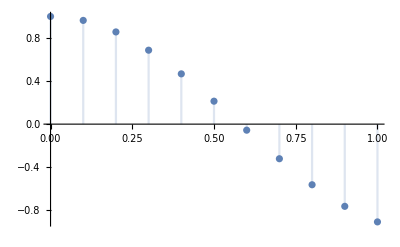

```mathematica
DiscretePlot[sim[data[[1]], k],{k, 0, 1, .1}]
```

```mathematica
amplitude[q, {1, 2}, q]
(*sim[data[[1]], 1]*)
```

2

```mathematica
sim[data[[1]], 1]
```

NDSolve::underdet: There are more dependent variables, {h[x,{0.,0.999884,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}],y[x]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{ⅈ y'[x]==h[x,{0.,0.999884,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}] y[x],y[0]==1/(√2)},y,{x,0,25.},MaxSteps→∞]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::underdet: There are more dependent variables, {h[x,{0.,0.999884,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}],y[x]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[{ⅈ y'[x]==-h[x,{0.,0.999884,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}] y[x],y[0]==1/(√2)},y,{x,0,25.},MaxSteps→∞]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{2 Re[y[25.]]^2,2 Im[y[25.]]^2}

```mathematica
y
```

y

```mathematica
sim[w, q]
```

Part::partd: Part specification w⟦1⟧ is longer than depth of object.

NDSolve::ndnl: Endpoint 25. q in {x,0.,25. q} is not a real number.

ReplaceAll::reps: {NDSolve[{ⅈ y'[x]==2 π Cos[1.5708+Times[«3»]] y[x],y[0]==1/(√2)},y,{x,0,25. q},MaxSteps→∞]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnl: Endpoint 25. q in {x,0.,25. q} is not a real number.

ReplaceAll::reps: {NDSolve[{ⅈ y'[x]==-2 π Cos[1.5708+Times[«3»]] y[x],y[0]==1/(√2)},y,{x,0,25. q},MaxSteps→∞]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{2 Re[y[25. q]]^2,2 Im[y[25. q]]^2}

```mathematica
{1,2}[[1]]
```

1